```mathematica
Sratio [ϕ_,Va_, Vt_,κ_]:=(ϕ-Vt-κ Va)^2/(2(ϕ-Vt)Va-Va^2)
```

```mathematica
Sratio[1.8, 0.3, 0.52, 1.4]
```

1.09086

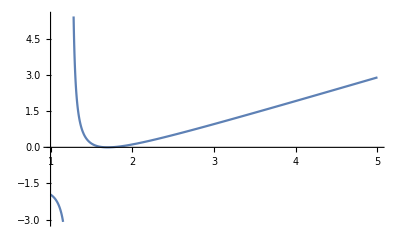

```mathematica
Va = 0.5; Vt = 1;
Plot[Sratio[ϕ,Va, Vt, 1.4],{ϕ, 1.0,5.0}]
```

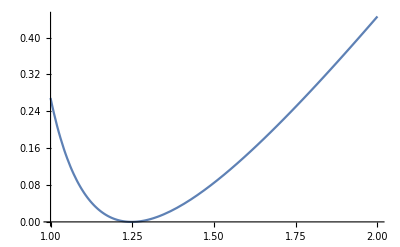

```mathematica
Va = 0.52; Vt = 0.52;
Plot[Sratio[ϕ,Va, Vt, 1.4],{ϕ, 1.0,2.0}]
```

```mathematica
Va = 0.4; Vt = 0.52;
Sratio[1.8,Va, Vt, 1.4]
```

0.6

```mathematica
Sratio1 [ϕ_,Va_, Vt_,κ_]:=(ϕ-Vt-κ Va)^2/(2κ(ϕ-Vt)Va-κ^2 Va^2)
```

```mathematica
Va = 0.4; Vt = 0.52;
Sratio1[1.8,Va, Vt, 1.4]
```

0.462857

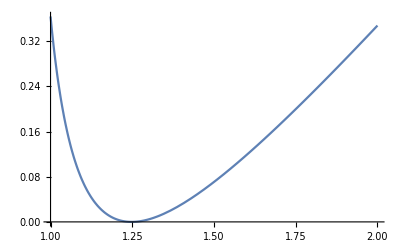

```mathematica
Va = 0.52; Vt = 0.52;
Plot[Sratio1[ϕ,Va, Vt, 1.4],{ϕ, 1.0,2.0}]
```

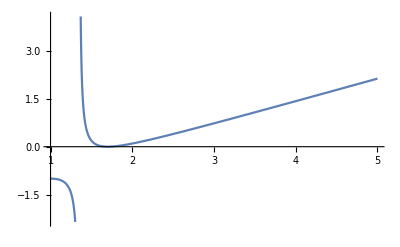

```mathematica
Va = 0.5; Vt = 1;
Plot[Sratio1[ϕ,Va, Vt, 1.4],{ϕ, 1.0,5.0}]
```